# Angular Crossing Collimated Flux

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
σT=6.65245871548*10^-29;
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Angles*)
fivedeg=(5*π)/180;
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

The optimised values within these cases are using the Compton_Optimisation_Parrallel.nb code, which is outdated (doesn’t include hourglass effect), but is the best for comparing to spectra etc.

```mathematica
CBETA150base={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
CBETA150opt={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.43333mrad};

DIANA687base={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.2,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.1mrad};
DIANA687opt={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.09181mrad};
```

## Integrated Cross Section Calculation

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.CBETA150opt
```

402516.

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol}];
```

```mathematica
σ[Ee,ϕ,λ,θcol]/.CBETA150base
```

2.08606×10^-30

```mathematica
σ[Ee,ϕ,λ,θcol]/.CBETA150opt
```

1.58358×10^-30

## Integrated Cross Section Investigation

## Integrated Cross Section Plots

```mathematica
σvsθCBETA150=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.CBETA150opt)/σT,(σ[Ee,ϕ,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(45*π)/180,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(90*π)/180,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(270*π)/180,λ,θ]/.CBETA150opt)/σT},{θ,-1/γ[Ee]/.CBETA150opt,1/γ[Ee]/.CBETA150opt,1/(100*γ[Ee])/.CBETA150opt}];
```

```mathematica
σvsθDIANA687=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.DIANA687opt)/σT,(σ[Ee,ϕ,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(45*π)/180,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(90*π)/180,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(270*π)/180,λ,θ]/.DIANA687opt)/σT},{θ,-1/γ[Ee]/.DIANA687opt,1/γ[Ee]/.DIANA687opt,1/(100*γ[Ee])/.DIANA687opt}];
```

```mathematica
csCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,2⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,3⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,4⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,5⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

```mathematica
csDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,2⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,3⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,4⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,5⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

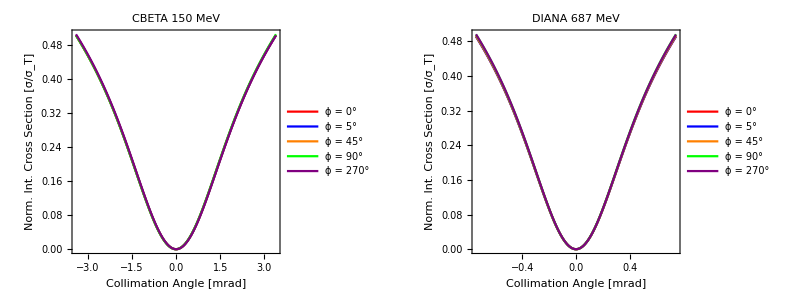

```mathematica
Grid[{{csCBETA150,csDIANA687}}]
```

## Integrated Cross Section Residuals

```mathematica
REScsCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T ×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.18,0.45}],ImageSize->Large];
```

```mathematica
REScsDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.4,0.25}],ImageSize->Large];
```

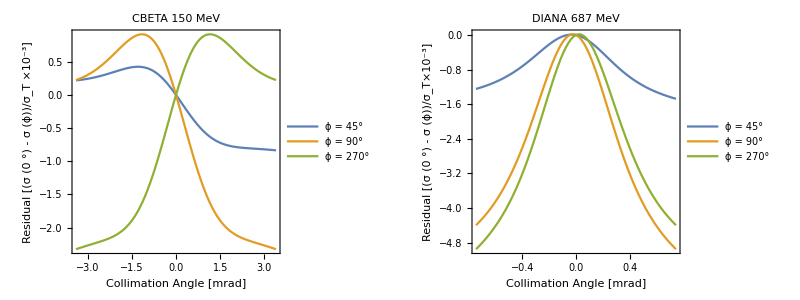

```mathematica
Grid[{{REScsCBETA150,REScsDIANA687}}]
```

## Collimated Flux Calculation [My Method]

## Collimated Flux Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(elecharge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Angular Crossing Luminosity Reduction Factor

```mathematica
RAC[βIP_,ϵn_,Ee_,σL_,ϕ_,σze_,tpulse_]:=(convxy[βIP,ϵn,Ee,σL]*Cos[ϕ])/Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ]^2+convz[σze,tpulse]^2*Sin[ϕ]^2];
```

## Collimated Flux [Me]

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Collimated Flux [My Method] Investigation

## CBETA Flux Cases

```mathematica
FcolCBETA150base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FcolCBETA150opt=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt},{θ,0,1/γ[Ee]/.CBETA150opt,1/(100*γ[Ee])/.CBETA150opt}];
```

```mathematica
baseFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,2⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% BW Optimised CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Optimised","Baseline"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

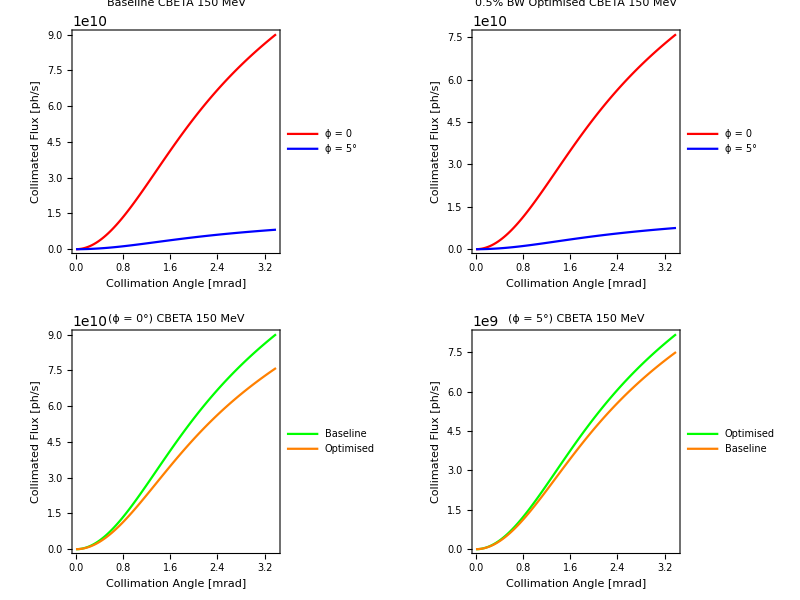

```mathematica
Grid[{{baseFcolCBETA,optFcolCBETA},{zerodegFcolCBETA,fivedegFcolCBETA}}]
```

## DIANA Flux Cases

```mathematica
FcolDIANA687base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
FcolDIANA687opt=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt},{θ,0,1/γ[Ee]/.DIANA687opt,1/(100*γ[Ee])/.DIANA687opt}];
```

```mathematica
baseFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,2⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% BW Optimised DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Optimised","Baseline"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

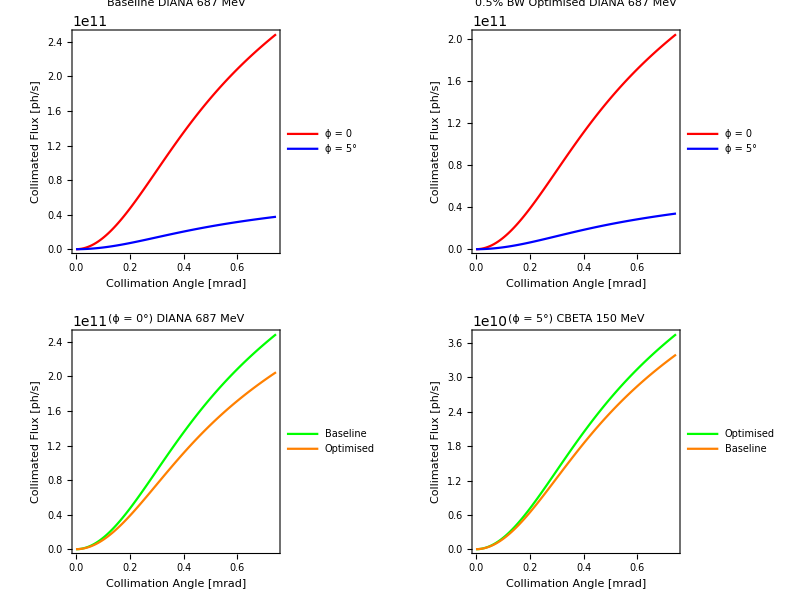

```mathematica
Grid[{{baseFcolDIANA,optFcolDIANA},{zerodegFcolDIANA,fivedegFcolDIANA}}]
```

## Collimated Flux Comparative Methods

## Collimated Flux Comparative Methods Intermediaries

```mathematica
(*Xrec is the recoil parameter in the head-on, ultra-relativistic case. Used in comparative sources - not mine!*) 
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
(*Cross section in the Thomson limit i.e as X->0*)
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
(*Rayleigh Range*)
zr[σL_,λ_]:=(4*π*σL^2)/λ;
(*Acceptance angle for Collimation Equations*)
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Curatolo F_ψ Method

```mathematica
FψCuratolo[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,θ_]:=σc[Ee,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

## Krafft F_(0.1%) Method

```mathematica
F01[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_]:=1.5*10^-3*σc[Ee,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```